```mathematica
calcClass[d_, inEms_, inSigmas_, inWs_] := 
(
iMax = 1;

For[ifP = 1, ifP ≤ Length[inEms], ifP++,
If[wp[d,inWs[[iMax]],inEms[[iMax]],inSigmas[[iMax]]] < wp[d,inWs[[ifP]],inEms[[ifP]],inSigmas[[ifP]]],
iMax = ifP;
];

];
iMax = iMax - 1;
iMax
);

colorF[czn_] := 
Piecewise[{{Lighter[Red, 2/3],-0.5≤czn≤0.5},{Lighter[Blue, 2/3],0.5<czn≤1.5},{Lighter[Green, 2/3],1.5<czn≤2.5}}];

forPaint[{xx_, yy_}, inEms_, inSigmas_, inWs_] := 
(
iMax = 1;

For[ifP = 1, ifP ≤ Length[inEms], ifP++,
If[wp[{xx,yy},inWs[[iMax]],inEms[[iMax]],inSigmas[[iMax]]] < wp[{xx,yy},inWs[[ifP]],inEms[[ifP]],inSigmas[[ifP]]],
iMax = ifP;
];

];
iMax = iMax - 1;
iMax
);

pj[x_,mo_,sig_]:=
(
summ = 0;
nmn = 1;
For[dcount=1,dcount≤ Length[mo], dcount++,
summ+= 1/sig[[dcount]] *(x[[dcount]] - mo[[dcount]])^2;
nmn /= (sig[[dcount]])^(1/2);
];

nmn*=(2 * Pi)^(-Length[mo]/2);

nmn*Exp[-1/2 * summ]
);

wp[x_,wq_,mo_,sig_]:=
(
Sum[wq[[t]] * pj[x,mo[[t]],sig[[t]]],{t,Length[mo]}]
);

TrainBayes[dataVectors_, componentsCount_] :=
(
Ems = {};
sigmas = {};
ws = {};

For[iBC = 1, iBC ≤  Length[dataVectors], iBC++,

fclass = dataVectors[[iBC]];
k =componentsCount[[iBC]]; (*это количество компонент смеси*)
ly = Length[fclass];(*размер выборки*)
r = Length[fclass[[1]]]; (*размерность пространства данных*)


(*kak yaponimayu sei4as eto razul'tat funkcii em*)
sigma = Table[1, {i, k}, {j, r}];
Em = Table[RandomReal[], {i, k}, {j,r}];



w = ConstantArray[1,k];(*начальное приближение весов*)

G = Table[0, {i,ly}, {j, k}];
sigma0 = sigma;
Em0 = Em;

minsigma = 0.0000000001;
delta = 0.00001;

While[True,
(*Е шаг*)


For[i = 1, i ≤  ly,i++,

pxi = Sum[ w[[s]] * pj[fclass[[i]], Em[[s]],sigma[[s]]], {s, k}];

For[j = 1, j ≤k,j++,
G[[i,j]] = w[[j]]*pj[fclass[[i]], Em[[j]],sigma[[j]]]/pxi;
];


(*здесь нормировка, хз надо ее или нет, пусть будет*)
dtemp = Sum[G[[i,j]],{j,k}];
For[j = 1, j ≤k,j++,
G[[i,j]] /= dtemp;
];

(*тут конец нормировки*)

];


(*Print["G = ", G];*)


(*М шаг*)

For[j = 1, j ≤ k, j++,

w[[j]] = Sum[G[[ic,j]], {ic, ly}]/ly;

(*вычисляем матожидание и дисперсию*)
For[d = 1, d ≤ r, d++,
Em[[j,d]]=Sum[G[[i,j]] * fclass[[i, d]], {i,ly}] / (ly * w[[j]]);

sigma[[j,d]]=Sum[G[[i,j]] * (fclass[[i, d]] - Em[[j,d]])^2, {i,ly}] / (ly* w[[j]]);
];

(*
For[c1 = 1, c1 ≤ k, c1++,
For[c2 = 1,c2 ≤ r, c2++,

If[sigma[[c1, c2]] < minsigma, 
PrintTemporary["i did it :", sigma[[c1,c2]], "   ", c1, "   ", c2]; 
sigma = Table[1, {i, k}, {j, r}];
Em = Table[RandomReal[], {i, k}, {j,r}];
];

];
];*)

];


(*вычисление невязки и конец цикла если что вдруг*)
nevyazka = Max[{Max[Table[Abs[sigma0[[i,j]]-sigma[[i,j]]],{i,k},{j,r}]],  Max[Table[Abs[Em0[[i,j]]-Em[[i,j]]],{i,k},{j,r}]]}  ];
sigma0 = sigma;
Em0 = Em;
If[nevyazka < delta, Break[]];
(*PrintTemporary[nevyazka]*)
(*Pause[0.1];*)
];

AppendTo[Ems, Em];
AppendTo[sigmas, sigma];
AppendTo[ws, w];
];

)
```

-Graphics3D-

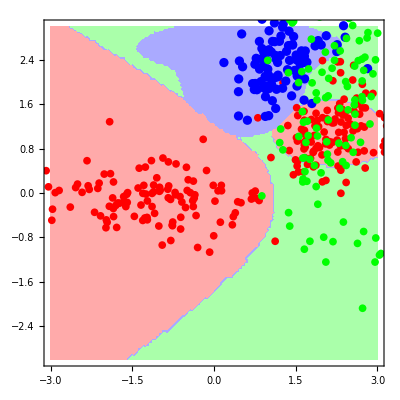

```mathematica
ssclass = {};
xs = RandomReal[]*6 - 3;
ys = RandomReal[]*6 - 3;
xd = RandomReal[] * 2 + 0.5;
yd = RandomReal[] * 2 + 0.5;
For[i = 1, i < 100, i++,
phi = RandomReal[];
rd = RandomReal[];
AppendTo[ssclass, {Cos[2*Pi*phi]*Sqrt[-2Log[rd]]/xd +xs,Sin[2*Pi*phi]*Sqrt[-2Log[rd]]/yd+ys}]
];

fclass={};
xs = RandomReal[]*6 - 3;
ys = RandomReal[]*6 - 3;
xd = RandomReal[] * 2+ 0.5;
yd = RandomReal[] * 2 + 0.5;
For[i = 1, i < 120, i++,
phi = RandomReal[];
rd = RandomReal[];
AppendTo[fclass, {Cos[2*Pi*phi]*Sqrt[-2Log[rd]]/xd+xs,Sin[2*Pi*phi]*Sqrt[-2Log[rd]]/yd+ys}]
];

xs = RandomReal[]*6 - 3;
ys = RandomReal[]*6 - 3;
xd = RandomReal[] * 2+ 0.5;
yd = RandomReal[] * 2+ 0.5;
For[i = 1, i < 120, i++,
phi = RandomReal[];
rd = RandomReal[];
AppendTo[fclass, {Cos[2*Pi*phi]*Sqrt[-2Log[rd]]/xd+xs,Sin[2*Pi*phi]*Sqrt[-2Log[rd]]/yd+ys}]
];

tclass={};
xs = RandomReal[]*6 - 3;
ys = RandomReal[]*6 - 3;
xd = RandomReal[] * 2 + 0.5;
yd = RandomReal[] * 2 + 0.5;
For[i = 1, i < 120, i++,
phi = RandomReal[];
rd = RandomReal[];
AppendTo[tclass, {Cos[2*Pi*phi]*Sqrt[-2Log[rd]]/xd + xs,Sin[2*Pi*phi]*Sqrt[-2Log[rd]]/yd + ys}]
];

data = {fclass, ssclass, tclass};
comp = {2,2, 2};
TrainBayes[data, comp];

Show[Plot3D[wp[{x,y},ws[[1]],Ems[[1]],sigmas[[1]]],{x,-3,3},{y,-3,3}, PlotStyle->{Red}, PlotRange->{0,1}],
Plot3D[wp[{x,y},ws[[2]],Ems[[2]],sigmas[[2]]],{x,-3,3},{y,-3,3}, PlotStyle->{Blue}, PlotRange->{0,1}],
Plot3D[wp[{x,y},ws[[3]],Ems[[3]],sigmas[[3]]],{x,-3,3},{y,-3,3}, PlotStyle->{Green}, PlotRange->{0,1}]
]
Show[ContourPlot[forPaint[{x,y}, Ems, sigmas, ws], {x, -3, 3},{y,-3,3}, ColorFunction->colorF,ColorFunctionScaling->False, PlotRange->All, ContourStyle->None],ListPlot[data[[1]], PlotStyle->{Red}],ListPlot[data[[2]], PlotStyle->{Blue}],ListPlot[data[[3]], PlotStyle->{Green}], PlotRange-> {{-3,3},{-3,3}}]
```

```mathematica
Ems
sigmas
ws
```

{{{0.489697,1.07047}},{{0.489697,1.07047}}}

```mathematica
GetParametersFromDNM[dnm_] := (
normalizedDNM = NormalizeDnm[dnm, {100,100},{0,0}];

parameters = FourierDecript[RnFunction[normalizedDNM]];

parameters
);
```